```mathematica
cf=Blend[{Red,Blue},#]&
```

```mathematica
cf[0]
cf[1]
```

## Scans

```mathematica
NotebooksPath="/Users/endres/Documents/MIT/research/bdeop/endres/ising/code_v0.6/Mathematica/";
```

```mathematica
NotebookEvaluate[NotebooksPath<>"/ising.nb"]
```

```mathematica
path="/Users/endres/Documents/MIT/research/bdeop/endres/ising/code_v0.6/tests/scan_twolevel/data";
```

```mathematica
sweeps=5;
Do[
m[j]=GetMagnetization[path<>"/magnetization_"<>ToString[j]<>".dat"];
h[j]=GetHamiltonian[path<>"/hamiltonian_"<>ToString[j]<>".dat"];
c[j]=GetCorrelator[path<>"/correlator_"<>ToString[j]<>".dat"];
,{j,0,sweeps-1}]
```

```mathematica
mPlot=ErrorListPlot[Table[m[j],{j,0,sweeps-1}],
PlotStyle->Table[cf[i/sweeps],{i,0,sweeps-1}],
FrameLabel->{"K","M"},
Epilog->{Black,Dashed,Thick,Line[{{Kcrit,-2},{Kcrit,2}}]}
]
```

```mathematica
hPlot=ErrorListPlot[Table[h[j],{j,0,sweeps-1}],
PlotStyle->Table[cf[i/sweeps],{i,0,sweeps-1}],
FrameLabel->{"K","E"},
Epilog->{Black,Dashed,Thick,Line[{{Kcrit,-2},{Kcrit,2}}]}
]
```

```mathematica
Do[
cPlot[k]=ErrorListPlot[Table[c[j][[k,2]],{j,0,sweeps-1}],
PlotStyle->Table[cf[i/sweeps],{i,0,sweeps-1}],
PlotRange->All,
PlotLabel->"K = "<>ToString[c[0][[k,1]]],
FrameLabel->{"τ","C"}
]
,{k,1,Length[c[0][[All,1]]]}]
```

```mathematica
GraphicsRow[
Table[cPlot[k],{k,35,55}]
]
```

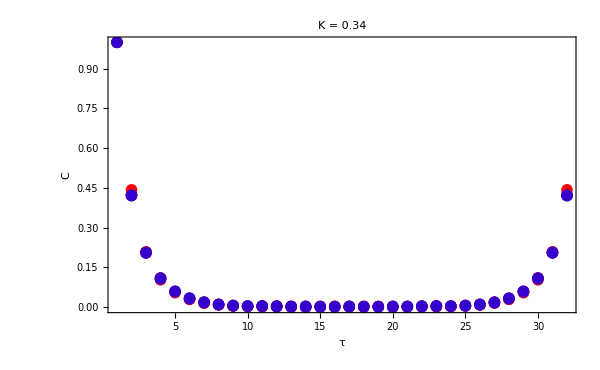
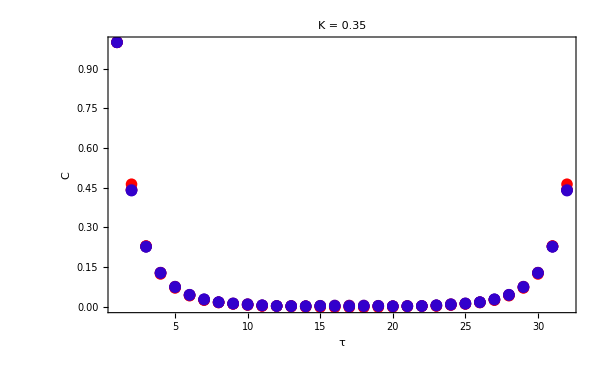
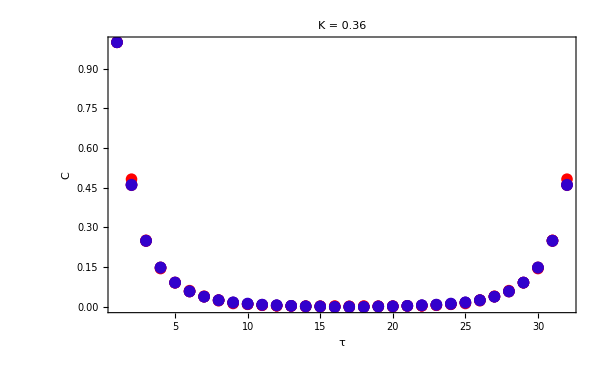
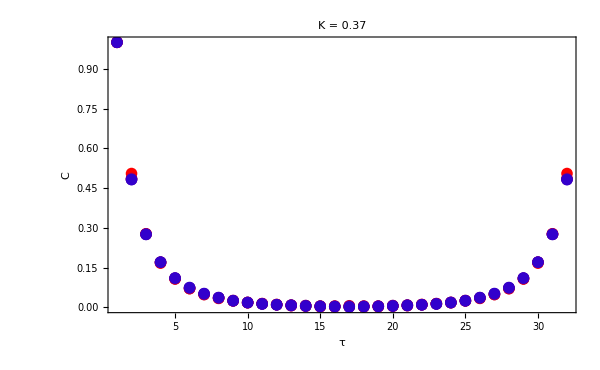
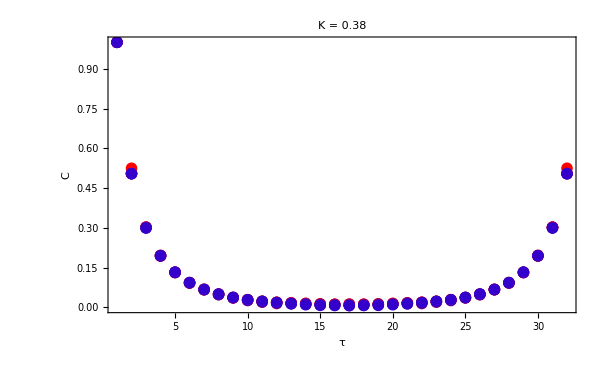
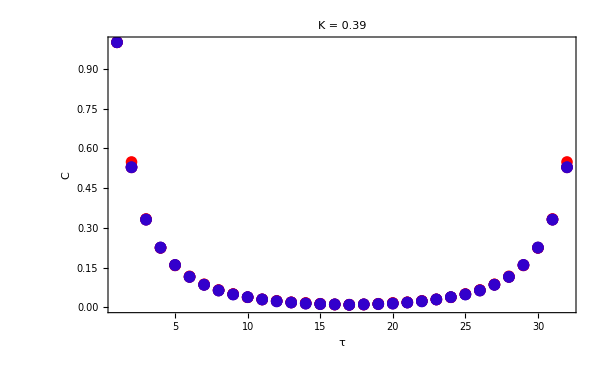
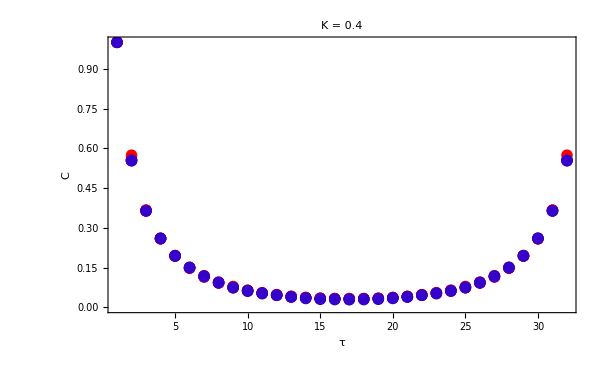
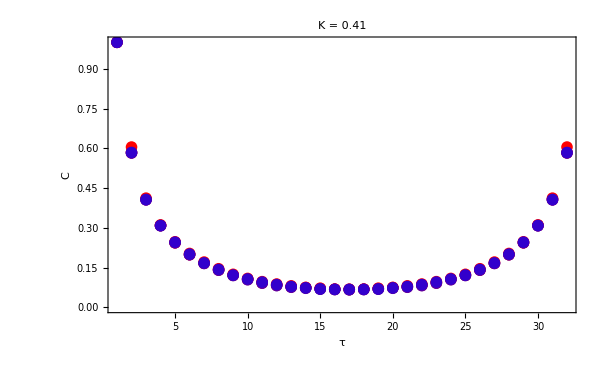

## Comparison

```mathematica
mx=GetMagnetization[path<>"/magnetization.dat"];
hx=GetHamiltonian[path<>"/hamiltonian.dat"];
cx=GetCorrelator[path<>"/correlator.dat"];
```

```mathematica
mxPlot=ErrorListPlot[mx,
PlotStyle->Black,
Joined->True,
FrameLabel->{"K","M"},
Epilog->{Black,Dashed,Thick,Line[{{Kcrit,-2},{Kcrit,2}}]}
];
```

```mathematica
hxPlot=ErrorListPlot[hx,
PlotStyle->Black,
Joined->True,
FrameLabel->{"K","M"},
Epilog->{Black,Dashed,Thick,Line[{{Kcrit,-2},{Kcrit,2}}]}
];
```

```mathematica
Do[
cxPlot[k]=ErrorListPlot[cx[[k,2]],
PlotStyle->Black,
Joined->True,
PlotRange->All,
PlotLabel->"K = "<>ToString[cx[[k,1]]],
FrameLabel->{"τ","C"}
]
,{k,1,Length[cx[[All,1]]]}]
```

```mathematica
Show[mPlot,mxPlot]
```

```mathematica
Show[hPlot,hxPlot]
```

```mathematica
GraphicsRow[
Table[Show[cPlot[k],cxPlot[k]],{k,35,55}]
]
```

```mathematica
GraphicsRow[
Table[Show[cPlot[k],cxPlot[k]],{k,60,80}]
]
```